## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
(*Q10 = 2.5; Average factor for biological systems*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_MD.csv";

mainFolder = "GAPD_param_inf2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{g3p,Null;nad,Null;pi,Null,Keq substrate}

{0.452,Keq value}

{nad,Km or S05 substrate}

{0.000045,Km or S05 value}

{g3p,Km or S05 substrate}

{0.00089,Km or S05 value}

{pi,Km or S05 substrate}

{0.00053,Km or S05 value}

{{{g3p,Null},{nad,Null},{pi,Null}},kcat substrates}

{268,kcat value}

{nad,Other parameter susbtrate}

{3.2×10^-7,Other parameter value}

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi
"[nad,g3p,pi,1,3-diphosphoglycerate,nadh]"

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1}
```

{{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}}

### Setup King-Altman Equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc=1;
simplifyFlag=True;
simplifyMaxTime=300;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites,assumedSaturatingConc];
```

{g3p^c→0,nad^c→0,pi^c→0}

{(13dpg)^c→0,nadh^c→0}

{g3p^c→1,nad^c→1,pi^c→1}

{(13dpg)^c→1,nadh^c→1}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
haldaneRatiosList
```

{(k_GAPD1^⟶ k_GAPD2^⟶ k_GAPD3^⟶ k_GAPD4^⟶ k_GAPD5^⟶ k_GAPD6^⟶)/(k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD3^⟵ k_GAPD4^⟵ k_GAPD5^⟵ k_GAPD6^⟵)}

```mathematica
enzymeModelOrig["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

## Semi-Automated Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵),0.5,{0.025, 9.9}}};
customRatiosDataList
```

{{1,(k_GAPD1^⟶ k_GAPD2^⟶ k_GAPD3^⟶ k_GAPD4^⟶)/(k_GAPD1^⟵ k_GAPD2^⟵ k_GAPD3^⟵ k_GAPD4^⟵),0.5,{0.025,9.9}}}

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/haldaneRatio_1.txt"	0.452
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	1	1	0	1	1	8.9	22	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/customRatio_1.txt"	0.5

### Simulate data with uncertainty

```mathematica
Export["GAPDSimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["GAPDSimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter influence

```mathematica
dataFileName = "GAPD_all";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];

dataFileName = "GAPD_dKd";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp={};
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];

dataFileName = "GAPD_Keq";
KeqListTemp={};
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  fitLabel,haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];

dataFileName = "GAPD_Km1";
KeqListTemp=KeqList;
kmListTemp=kmList[[2;;]];
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  fitLabel, haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];


dataFileName = "GAPD_Km2";
KeqListTemp=KeqList;
kmListTemp={kmList[[1]], kmList[[3]]};
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  fitLabel, haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];


dataFileName = "GAPD_Km3";
KeqListTemp=KeqList;
kmListTemp=kmList[[;;2]];
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  fitLabel, haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];


dataFileName = "GAPD_kcat";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = {};
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = otherParmsList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  fitLabel, haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];

dataFileName = "GAPD_Kd";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;
otherParmsListTemp = {};

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsListTemp, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Do::iterb: Iterator {MASSef`Private`customRatio,customRatiosDataList} does not have appropriate bounds.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Do::iterb: Iterator {MASSef`Private`customRatio,customRatiosDataList} does not have appropriate bounds.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Do::iterb: Iterator {MASSef`Private`customRatio,customRatiosDataList} does not have appropriate bounds.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Do::iterb: Iterator {MASSef`Private`customRatio,customRatiosDataList} does not have appropriate bounds.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Do::iterb: Iterator {MASSef`Private`customRatio,customRatiosDataList} does not have appropriate bounds.

Simulating Keq data...

Simulating Km data...

Simulating other data...

Simulating custom ratios data...

Do::iterb: Iterator {MASSef`Private`customRatio,customRatiosDataList} does not have appropriate bounds.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Do::iterb: Iterator {MASSef`Private`customRatio,customRatiosDataList} does not have appropriate bounds.

### Parameter scan

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,10.^-5,0.0001,0.001, 0.01,0.1,0.5, 1.0,  10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/haldaneRatio_1.txt"	0.452
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.
1	0	0	0	0	0	1	7	25	"/home/mrama/Desktop/MD/kinetics/GAPD/GAPD_param_scan/input/customRatio_1.txt"	10000.

## Configure the Particle Swarm Optimization and Levenberg-MarquardDropboxt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

Traceback (most recent call last):
  File "/home/mrama/Desktop/MASSef/python_code/src/run_fit_rel.py", line 62, in <module>
    run_pso(pso_parameters, data_file_name, pso_summary_file_name, pso_ultimate_result_file_name)
  File "/home/mrama/Desktop/MASSef/python_code/src/pso_short_ver0091_rel_marta.py", line 457, in run_pso
    (header, data) = load_enzyme_data(data_file_name)
  File "/home/mrama/Desktop/MASSef/python_code/src/pso_short_ver0091_rel_marta.py", line 27, in load_enzyme_data
    lines = open(path).readlines()
IOError: [Errno 2] No such file or directory: '/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/GAPD_Kd_GAPD.dat'

## Pull in Parameters and Check Fit and Enzyme Statistics for param_scan

```mathematica
outputPath
```

/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_scan2/output

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0,  10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

nEnsembles=10;

flagFitType = "log_ssd";
errorList = {};
Do[
Do[

fitDescription = paramScan[[1]] <>"_"<>ToString[paramScan[[2]]]<>"_"<> ToString[N@AccountingForm[paramVal]];
ssdList = 
Table[

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> "_"<>ToString@ensembleI<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "GAPD_"<> fitDescription<>".dat"}, OperatingSystem->$OperatingSystem];

{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription<>"_"<>ToString[ensembleI]];

ToString[N@AccountingForm[filteredDataList[[1,1]]]],

{ensembleI, Range[nEnsembles]}];

Print[ssdList];
AppendTo[errorList, Flatten@{ToString[N@AccountingForm[paramVal]], ssdList}];,

{paramVal, paramScan[[3]]}];,
{paramScan, paramScanList}];

Export[ FileNameJoin[{outputPath, "treated_data", "param_scan_ssd.csv"}, OperatingSystem->$OperatingSystem],errorList, "TSV"];
```

{602816.,606403.,609002.,591909.,602869.,604426.,604149.,606742.,601324.,598296.}

{482346.,470825.,483365.,479624.,460157.,478058.,476387.,483102.,482059.,478815.}

{296099.,292829.,293120.,216659.,281385.,283776.,277339.,280750.,281579.,289970.}

{81556.8,68131.2,64661.,67218.7,58171.4,62664.7,30491.6,65443.4,73365.1,66085.}

{0.000437261,0.000472864,0.0260456,0.0964245,0.0961911,0.0963332,0.000622984,0.00189119,0.094308,0.096386}

{0.0000017504,0.00000177419,0.00000177257,0.00000177459,0.00000177703,0.00000176952,0.00000177362,0.00000177388,0.00000176861,0.00000176847}

{0.00000176749,0.00000176536,0.0000017558,0.0000017692,0.00000176083,0.00000176405,0.00000176711,0.00000176676,0.0000017634,0.00000175796}

{0.00000176984,0.00000176363,0.00000176957,0.00000176472,0.00000175782,0.00000175904,0.00000177568,0.00000176409,0.00000176332,0.00000177071}

{0.00000175859,0.00000166045,0.00000176077,0.00000176529,0.00000176518,0.00000176145,0.00000175924,0.0000017636,0.00000174993,0.00000176628}

{0.00000176328,0.00000175892,0.00000176621,0.00000176185,0.00000175859,0.00000175905,0.00000165146,0.00000177417,0.00000176135,0.00000175977}

{0.00000176335,0.00000173235,0.00000175715,0.00000176283,0.00000176586,0.00000176169,0.00000175776,0.00000176448,0.00000176068,0.00000175713}

{0.00000168101,0.00000176391,0.00000158463,0.00000176319,0.00000176181,0.00000175791,0.00000176196,0.00000175802,0.00000177042,0.0000017246}

{0.00000176114,0.00000176813,0.00000176409,0.00000175891,0.00000176692,0.00000176393,0.00000175275,0.00000175788,0.00000176054,0.00000176653}

{0.00000177114,0.00000177084,0.00000177138,0.00000177116,0.00000177026,0.00000177048,0.00000177237,0.00000177356,0.00000177049,0.00000177099}

{0.00000177627,0.00000177568,0.00000177545,0.00000174053,0.00000177622,0.00000177558,0.0000017758,0.00000177574,0.00000177664,0.00000177577}

$Aborted

```mathematica
errorList//TableForm
```

0.000000000001 | 602816. | 606403. | 609002. | 591909. | 602869. | 604426. | 604149. | 606742. | 601324. | 598296.
0.00000000001 | 482346. | 470825. | 483365. | 479624. | 460157. | 478058. | 476387. | 483102. | 482059. | 478815.
0.0000000001 | 296099. | 292829. | 293120. | 216659. | 281385. | 283776. | 277339. | 280750. | 281579. | 289970.
0.000000001 | 81556.8 | 68131.2 | 64661. | 67218.7 | 58171.4 | 62664.7 | 30491.6 | 65443.4 | 73365.1 | 66085.
0.00000001 | 0.000437261 | 0.000472864 | 0.0260456 | 0.0964245 | 0.0961911 | 0.0963332 | 0.000622984 | 0.00189119 | 0.094308 | 0.096386
0.0000001 | 0.0000017504 | 0.00000177419 | 0.00000177257 | 0.00000177459 | 0.00000177703 | 0.00000176952 | 0.00000177362 | 0.00000177388 | 0.00000176861 | 0.00000176847
0.000001 | 0.00000176749 | 0.00000176536 | 0.0000017558 | 0.0000017692 | 0.00000176083 | 0.00000176405 | 0.00000176711 | 0.00000176676 | 0.0000017634 | 0.00000175796
0.00001 | 0.00000176984 | 0.00000176363 | 0.00000176957 | 0.00000176472 | 0.00000175782 | 0.00000175904 | 0.00000177568 | 0.00000176409 | 0.00000176332 | 0.00000177071
0.0001 | 0.00000175859 | 0.00000166045 | 0.00000176077 | 0.00000176529 | 0.00000176518 | 0.00000176145 | 0.00000175924 | 0.0000017636 | 0.00000174993 | 0.00000176628
0.001 | 0.00000176328 | 0.00000175892 | 0.00000176621 | 0.00000176185 | 0.00000175859 | 0.00000175905 | 0.00000165146 | 0.00000177417 | 0.00000176135 | 0.00000175977
0.01 | 0.00000176335 | 0.00000173235 | 0.00000175715 | 0.00000176283 | 0.00000176586 | 0.00000176169 | 0.00000175776 | 0.00000176448 | 0.00000176068 | 0.00000175713
0.1 | 0.00000168101 | 0.00000176391 | 0.00000158463 | 0.00000176319 | 0.00000176181 | 0.00000175791 | 0.00000176196 | 0.00000175802 | 0.00000177042 | 0.0000017246
1. | 0.00000176114 | 0.00000176813 | 0.00000176409 | 0.00000175891 | 0.00000176692 | 0.00000176393 | 0.00000175275 | 0.00000175788 | 0.00000176054 | 0.00000176653
10. | 0.00000177114 | 0.00000177084 | 0.00000177138 | 0.00000177116 | 0.00000177026 | 0.00000177048 | 0.00000177237 | 0.00000177356 | 0.00000177049 | 0.00000177099
100. | 0.00000177627 | 0.00000177568 | 0.00000177545 | 0.00000174053 | 0.00000177622 | 0.00000177558 | 0.0000017758 | 0.00000177574 | 0.00000177664 | 0.00000177577
1000. | 197302. | 195819. | 200688. | 174.762 | 75281.6 | 173433. | 134.377 | 194627. | 196869. | 13475.3
10000. | 196259874. | 50.4075 | 198954188. | 170836018. | 190749834. | 161471269. | 203765612. | 255011. | 185362896. | 187512901.
100000. | 46161319774. | 40764059905. | 48868305958. | 35857793632. | 4624634688. | 1191684189. | 47684757139. | 48289881337. | 47966909327. | 48176477590.
1000000. | 6975466404693. | 1605228253657. | 5721387830500. | 182758342138. | 2454351507237. | 864378363745. | 6523353618347. | 1050761794639. | 190068386176. | 7031590041429.
10000000. | 147594556002683. | 406973041862162. | 358159573946122. | 390023441959791. | 340637653875950. | 359854346327014. | 371317740385782. | 357183572563286. | 347821279622602. | 366464524711960.
100000000. | 68799853898813150. | 46262909324808560. | 50504831952101820. | 33607122934297290. | 49245037877940260. | 58016202754056440. | 68906300906696440. | 67552584302044300. | 69541705640201900. | 35639844546424060.
1000000000. | 7789382297794054000. | 8169728229892380000. | 7795432799951490000. | 8414251831117770000. | 8536965564298730000. | 8532746089259170000. | 8286954723651550000. | 7812970230099128000. | 7774505436841203000. | 7881942748413890000.
10000000000. | 932006332417901000000. | 978125651247923000000. | 929159149623758000000. | 930152240365752000000. | 972726548729019000000. | 972674411358742000000. | 956832429171643000000. | 982340147895091000000. | 981824140806206000000. | 981686929013845000000.
100000000000. | 102938428145289400000000. | 102712331162419800000000. | 102566473139776200000000. | 102774670543617200000000. | 103045345628109000000000. | 102643718740696600000000. | 102697331519194100000000. | 102715808690392800000000. | 101883034173988500000000. | 101882639755710100000000.
1000000000000. | 10694339765205880000000000. | 10696930260678290000000000. | 10679437782047970000000000. | 10691048838837550000000000. | 10683320546067930000000000. | 10696032901787050000000000. | 10697152134679250000000000. | 10692764695107010000000000. | 10721472436535540000000000. | 10697415887635760000000000.

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | haldaneRatio_1 | 1.8579 | 3.45177 | 32.1342 | 7109.34 | 0.452 | 32.5862
1 | relRateFor_nad | 2.05346 | 4.21671 | 0.0901053 | 99.1158 | 0.0909091 | 0.000803795
1 | relRateFor_nad | 2.03117 | 4.12563 | 0.135534 | 99.0692 | 0.136807 | 0.00127333
1 | relRateFor_nad | 1.99806 | 3.99223 | 0.198743 | 98.9955 | 0.20076 | 0.0020166
1 | relRateFor_nad | 1.95035 | 3.80386 | 0.281555 | 98.8789 | 0.284747 | 0.00319236
1 | relRateFor_nad | 1.88425 | 3.5504 | 0.381813 | 98.6946 | 0.386863 | 0.00505017
1 | relRateFor_nad | 1.79694 | 3.22899 | 0.492019 | 98.4039 | 0.5 | 0.00798054
1 | relRateFor_nad | 1.68754 | 2.84778 | 0.600547 | 97.9466 | 0.613137 | 0.0125899
1 | relRateFor_nad | 1.55761 | 2.42614 | 0.695444 | 97.2306 | 0.715253 | 0.0198085
1 | relRateFor_nad | 1.4108 | 1.99036 | 0.768203 | 96.1167 | 0.79924 | 0.0310368
1 | relRateFor_nad | 1.252 | 1.5675 | 0.814875 | 94.4024 | 0.863193 | 0.0483179
1 | relRateFor_nad | 1.08654 | 1.18056 | 0.834606 | 91.8066 | 0.909091 | 0.0744854
1 | relRateFor_g3p | 0.0328335 | 0.00107804 | 0.00713937 | 7.85331 | 0.0909091 | 0.0980485
1 | relRateFor_g3p | 0.0311342 | 0.000969339 | 0.0101677 | 7.43214 | 0.136807 | 0.146975
1 | relRateFor_g3p | 0.0287775 | 0.000828146 | 0.0137535 | 6.85074 | 0.20076 | 0.214514
1 | relRateFor_g3p | 0.0257019 | 0.000660586 | 0.0173602 | 6.0967 | 0.284747 | 0.302107
1 | relRateFor_g3p | 0.0219914 | 0.000483624 | 0.0200941 | 5.19411 | 0.386863 | 0.406957
1 | relRateFor_g3p | 0.0179173 | 0.000321028 | 0.0210594 | 4.21188 | 0.5 | 0.521059
1 | relRateFor_g3p | 0.0138809 | 0.00019268 | 0.0199136 | 3.24783 | 0.613137 | 0.63305
1 | relRateFor_g3p | 0.0102697 | 0.000105467 | 0.0171151 | 2.39287 | 0.715253 | 0.732368
1 | relRateFor_g3p | 0.00732195 | 0.0000536109 | 0.0135889 | 1.70023 | 0.79924 | 0.812829
1 | relRateFor_g3p | 0.00509067 | 0.000025915 | 0.0101776 | 1.17907 | 0.863193 | 0.873371
1 | relRateFor_g3p | 0.00349637 | 0.0000122246 | 0.00734836 | 0.808319 | 0.909091 | 0.916439
1 | relRateFor_pi | 1.82796 | 3.34144 | 0.0895581 | 98.5139 | 0.0909091 | 0.00135098
1 | relRateFor_pi | 1.80579 | 3.26088 | 0.134667 | 98.4361 | 0.136807 | 0.00213953
1 | relRateFor_pi | 1.77288 | 3.14311 | 0.197373 | 98.313 | 0.20076 | 0.00338685
1 | relRateFor_pi | 1.72549 | 2.97731 | 0.27939 | 98.1185 | 0.284747 | 0.00535761
1 | relRateFor_pi | 1.65989 | 2.75524 | 0.378397 | 97.8117 | 0.386863 | 0.00846574
1 | relRateFor_pi | 1.57337 | 2.47548 | 0.486646 | 97.3292 | 0.5 | 0.0133538
1 | relRateFor_pi | 1.4652 | 2.14681 | 0.59213 | 96.5739 | 0.613137 | 0.0210066
1 | relRateFor_pi | 1.3372 | 1.7881 | 0.682348 | 95.3995 | 0.715253 | 0.0329048
1 | relRateFor_pi | 1.19337 | 1.42414 | 0.748036 | 93.5934 | 0.79924 | 0.0512038
1 | relRateFor_pi | 1.03913 | 1.07978 | 0.78431 | 90.8615 | 0.863193 | 0.0788827
1 | relRateFor_pi | 0.880463 | 0.775216 | 0.789377 | 86.8315 | 0.909091 | 0.119714
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | absRateFor | 2.42355 | 5.8736 | 266.989 | 99.6229 | 268 | 1.01061
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | KdRatio_nad | 0.540356 | 0.291984 | 2.27787×10^-7 | 71.1833 | 3.2×10^-7 | 9.22135×10^-8
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10
1 | customRatio_1 | 1.85856 | 3.45424 | 9.8615×10^11 | 98.615 | 1.×10^12 | 1.38497×10^10

#### Export rate back calculated parameter error distribution

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;

Do[
Do[
rateConstList=Import[outputPath<>"/treated_data/rateconst_GAPD_customRatio_1_"<> ToString[N@AccountingForm[paramVal]]<>"_"<>ToString[ensembleI]<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]],
backCalculateRatios[customRatiosDataList[[1,2]],paramVal,  paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_nad","Km_g3p", "Km_pi", "kcat_f","Keq", "dKd"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kmList[[2]][[3]], kmList[[3]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]], customRatiosDataList[[1,3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<> ToString[N@AccountingForm[paramVal]]<>"_"<>ToString[ensembleI]<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];,

{ensembleI, Range[nEnsembles]}];,

{paramVal, paramScanList[[1,3]]}];




Do[
Do[
rateConstList=Import[outputPath<>"/treated_data/rateconst_GAPD_customRatio_1_"<> ToString[N@AccountingForm[paramVal]]<>"_"<>ToString[ensembleI]<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]],
backCalculateRatios[customRatiosDataList[[1,2]],paramVal,  paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_nad","Km_g3p", "Km_pi", "kcat_f","Keq", "dKd"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kmList[[2]][[3]], kmList[[3]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]], customRatiosDataList[[1,3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution_"<> ToString[N@AccountingForm[paramVal]]<>"_"<>ToString[ensembleI]<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];,

{ensembleI, Range[nEnsembles]}];,

{paramVal, paramScanList[[1,3]]}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

### Simulated Data and Best Fit Data Plot

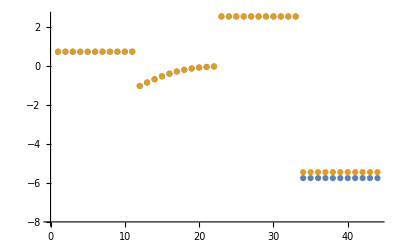

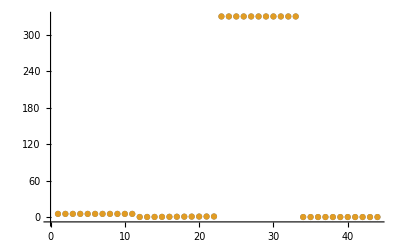

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10

## Pull in Parameters and Check Fit and Enzyme Statistics for param_inf

```mathematica
paramList={"all", "dKd", "kcat", "Keq", "Km1", "Km2", "Km3", "Kd"};
nEnsembles = 99;
flagFitType = "log_ssd";
```

```mathematica
lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> ".txt"}, OperatingSystem->$OperatingSystem];
```

```mathematica
Do[
Do[

fitDescription = param <>"_"<>ToString[fitI];

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "GAPD_"<> param<> ".dat"}, OperatingSystem->$OperatingSystem];

{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription<>"_"<>flagFitType];,

{fitI, 0, nEnsembles}],
{param, paramList}];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | relRateFor_2pg | 4.72843×10^-7 | 2.2358×10^-13 | 9.89783×10^-8 | 0.000108876 | 0.0909091 | 0.0909092
1 | relRateFor_2pg | 4.4897×10^-7 | 2.01574×10^-13 | 1.4143×10^-7 | 0.000103379 | 0.136807 | 0.136807
1 | relRateFor_2pg | 4.15706×10^-7 | 1.72812×10^-13 | 1.92167×10^-7 | 0.00009572 | 0.20076 | 0.20076
1 | relRateFor_2pg | 3.72022×10^-7 | 1.38401×10^-13 | 2.43918×10^-7 | 0.0000856614 | 0.284747 | 0.284747
1 | relRateFor_2pg | 3.18909×10^-7 | 1.01703×10^-13 | 2.8408×10^-7 | 0.0000734316 | 0.386863 | 0.386863
1 | relRateFor_2pg | 2.60064×10^-7 | 6.76331×10^-14 | 2.99409×10^-7 | 0.0000598819 | 0.5 | 0.5
1 | relRateFor_2pg | 2.01218×10^-7 | 4.04887×10^-14 | 2.8408×10^-7 | 0.0000463322 | 0.613137 | 0.613137
1 | relRateFor_2pg | 1.48105×10^-7 | 2.1935×10^-14 | 2.43918×10^-7 | 0.0000341024 | 0.715253 | 0.715253
1 | relRateFor_2pg | 1.04421×10^-7 | 1.09037×10^-14 | 1.92167×10^-7 | 0.0000240438 | 0.79924 | 0.79924
1 | relRateFor_2pg | 7.1157×10^-8 | 5.06331×10^-15 | 1.4143×10^-7 | 0.0000163845 | 0.863193 | 0.863193
1 | relRateFor_2pg | 4.72843×10^-8 | 2.2358×10^-15 | 9.89782×10^-8 | 0.0000108876 | 0.909091 | 0.909091
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6

#### Export rate back calculated parameter error distribution

```mathematica
outputPath<>"/treated_data/rateconst_GAPD_"<> "all"<>"_"<>ToString[1]<>"_"<>flagFitType<>".csv"
```

/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/output/treated_data/rateconst_GAPD_all_1_log_ssd.csv

```mathematica
KdRatio =Values@FilterRules[fileListSub, "/home/mrama/Desktop/MD/eMASS-MD_complete_data/enzyme_models/GAPD/GAPD_param_inf2/input/KdRatio_nad.txt"]
```

{k_GAPD1^⟵/k_GAPD1^⟶}

```mathematica
otherParmsList[[1,4]]
```

3.2×10^-7

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;

Do[
Do[
rateConstList=Import[outputPath<>"/treated_data/rateconst_GAPD_"<> param<>"_"<>ToString[ensembleI](*<>"_"<>flagFitType*)<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,3]],
backCalculateRatios[KdRatio[[1]],otherParmsList[[1,4]],  paramFitSub][[2,3]],
backCalculateRatios[customRatiosDataList[[1,2]],customRatiosDataList[[1,3]],  paramFitSub][[2,3]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_nad","Km_g3p", "Km_pi", "kcat_f","Keq","Kd", "dKd"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kmList[[2]][[3]], kmList[[3]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]], otherParmsList[[1,4]], customRatiosDataList[[1,3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<> param<>"_"<>ToString[ensembleI]<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];,

{ensembleI,0, nEnsembles}];,

{param, paramList}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Do[
Do[
rateConstList=Import[outputPath<>"/treated_data/rateconst_GAPD_"<> param<>"_"<>ToString[ensembleI]<>".csv", "TSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];

{rateConstList[[rateSetI,1]],
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName][[2;;,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2,2]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2,2]],
backCalculateRatios[customRatiosDataList[[1,2]],customRatiosDataList[[1,3]],  paramFitSub][[2,2]]}//Flatten,

{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","Km_nad","Km_g3p", "Km_pi", "kcat_f","Keq", "dKd"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,{0,kmList[[1]][[3]],kmList[[2]][[3]], kmList[[3]][[3]],kcatList[[1]][[3]], KeqList[[1]][[3]], customRatiosDataList[[1,3]]}  ,2];
Export[outputPath<>"/treated_data/predicted_params_distribution_"<> param<>"_"<>ToString[ensembleI]<>"_"<>flagFitType<>".csv",predictedParamsErrorList,"CSV"];,

{ensembleI,0, nEnsembles}];,

{param,paramList}];
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1,2;;All⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,2;;All⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

$Aborted

### Simulated Data and Best Fit Data Plot

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

-Graphics-

-Graphics-

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

-Graphics-

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

-Graphics-

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

-Graphics-

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

-Graphics-

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/GAPD.dat⟦2⟧ is longer than depth of object.

Part::partd: Part specification \"\</home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/GAPD.dat\>\"⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | haldaneRatio_1 | 1.38339×10^-12 | 1.91378×10^-24 | 1.43979×10^-12 | 3.18538×10^-10 | 0.452 | 0.452
1 | relRateFor_nad | 1.05693×10^-12 | 1.11711×10^-24 | 2.21226×10^-13 | 2.43348×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_nad | 1.0032×10^-12 | 1.00641×10^-24 | 3.16053×10^-13 | 2.31021×10^-10 | 0.136807 | 0.136807
1 | relRateFor_nad | 9.29146×10^-13 | 8.63312×10^-25 | 4.29518×10^-13 | 2.13946×10^-10 | 0.20076 | 0.20076
1 | relRateFor_nad | 8.31446×10^-13 | 6.91302×10^-25 | 5.4512×10^-13 | 1.9144×10^-10 | 0.284747 | 0.284747
1 | relRateFor_nad | 7.12708×10^-13 | 5.07952×10^-25 | 6.34881×10^-13 | 1.6411×10^-10 | 0.386863 | 0.386863
1 | relRateFor_nad | 5.81202×10^-13 | 3.37795×10^-25 | 6.69131×10^-13 | 1.33826×10^-10 | 0.5 | 0.5
1 | relRateFor_nad | 4.49724×10^-13 | 2.02251×10^-25 | 6.34937×10^-13 | 1.03555×10^-10 | 0.613137 | 0.613137
1 | relRateFor_nad | 3.30985×10^-13 | 1.09551×10^-25 | 5.4512×10^-13 | 7.62135×10^-11 | 0.715253 | 0.715253
1 | relRateFor_nad | 2.33411×10^-13 | 5.44805×10^-26 | 4.29545×10^-13 | 5.37442×10^-11 | 0.79924 | 0.79924
1 | relRateFor_nad | 1.59039×10^-13 | 2.52935×10^-26 | 3.1608×10^-13 | 3.66176×10^-11 | 0.863193 | 0.863193
1 | relRateFor_nad | 1.05596×10^-13 | 1.11505×10^-26 | 2.21045×10^-13 | 2.4315×10^-11 | 0.909091 | 0.909091
1 | relRateFor_g3p | 2.17788×10^-11 | 4.74316×10^-22 | 4.55888×10^-12 | 5.01477×10^-9 | 0.0909091 | 0.0909091
1 | relRateFor_g3p | 2.06792×10^-11 | 4.27631×10^-22 | 6.51415×10^-12 | 4.76157×10^-9 | 0.136807 | 0.136807
1 | relRateFor_g3p | 1.91472×10^-11 | 3.66617×10^-22 | 8.85111×10^-12 | 4.4088×10^-9 | 0.20076 | 0.20076
1 | relRateFor_g3p | 1.71351×10^-11 | 2.93611×10^-22 | 1.12347×10^-11 | 3.94551×10^-9 | 0.284747 | 0.284747
1 | relRateFor_g3p | 1.46888×10^-11 | 2.15761×10^-22 | 1.30845×10^-11 | 3.38221×10^-9 | 0.386863 | 0.386863
1 | relRateFor_g3p | 1.19784×10^-11 | 1.43483×10^-22 | 1.37906×10^-11 | 2.75813×10^-9 | 0.5 | 0.5
1 | relRateFor_g3p | 9.26789×10^-12 | 8.58938×10^-23 | 1.30844×10^-11 | 2.13401×10^-9 | 0.613137 | 0.613137
1 | relRateFor_g3p | 6.82163×10^-12 | 4.65346×10^-23 | 1.12347×10^-11 | 1.57073×10^-9 | 0.715253 | 0.715253
1 | relRateFor_g3p | 4.80951×10^-12 | 2.31314×10^-23 | 8.85103×10^-12 | 1.10743×10^-9 | 0.79924 | 0.79924
1 | relRateFor_g3p | 3.27746×10^-12 | 1.07418×10^-23 | 6.51423×10^-12 | 7.54667×10^-10 | 0.863193 | 0.863193
1 | relRateFor_g3p | 2.17801×10^-12 | 4.74372×10^-24 | 4.55913×10^-12 | 5.01504×10^-10 | 0.909091 | 0.909091
1 | relRateFor_pi | 1.21145×10^-11 | 1.46762×10^-22 | 2.53586×10^-12 | 2.78945×10^-9 | 0.0909091 | 0.0909091
1 | relRateFor_pi | 1.15028×10^-11 | 1.32314×10^-22 | 3.62352×10^-12 | 2.64864×10^-9 | 0.136807 | 0.136807
1 | relRateFor_pi | 1.06508×10^-11 | 1.1344×10^-22 | 4.92351×10^-12 | 2.45243×10^-9 | 0.20076 | 0.20076
1 | relRateFor_pi | 9.53138×10^-12 | 9.08471×10^-23 | 6.24933×10^-12 | 2.1947×10^-9 | 0.284747 | 0.284747
1 | relRateFor_pi | 8.17069×10^-12 | 6.67601×10^-23 | 7.27834×10^-12 | 1.88137×10^-9 | 0.386863 | 0.386863
1 | relRateFor_pi | 6.66311×10^-12 | 4.43971×10^-23 | 7.6712×10^-12 | 1.53424×10^-9 | 0.5 | 0.5
1 | relRateFor_pi | 5.15532×10^-12 | 2.65773×10^-23 | 7.27829×10^-12 | 1.18706×10^-9 | 0.613137 | 0.613137
1 | relRateFor_pi | 3.79452×10^-12 | 1.43984×10^-23 | 6.24933×10^-12 | 8.73724×10^-10 | 0.715253 | 0.715253
1 | relRateFor_pi | 2.67536×10^-12 | 7.15755×10^-24 | 4.92351×10^-12 | 6.16023×10^-10 | 0.79924 | 0.79924
1 | relRateFor_pi | 1.82306×10^-12 | 3.32353×10^-24 | 3.62343×10^-12 | 4.19771×10^-10 | 0.863193 | 0.863193
1 | relRateFor_pi | 1.21139×10^-12 | 1.46747×10^-24 | 2.53575×10^-12 | 2.78932×10^-10 | 0.909091 | 0.909091
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | absRateFor | 1.66134×10^-12 | 2.76004×10^-24 | 1.02511×10^-9 | 3.82505×10^-10 | 268 | 268.
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | KdRatio_nad | 0.382427 | 0.14625 | 4.51928×10^-7 | 141.227 | 3.2×10^-7 | 7.71928×10^-7
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6
1 | customRatio_1 | 0.0917584 | 0.0084196 | 2.56433×10^-7 | 23.526 | 1.09×10^-6 | 1.34643×10^-6

### Simulated Data and Best Fit Data Plot

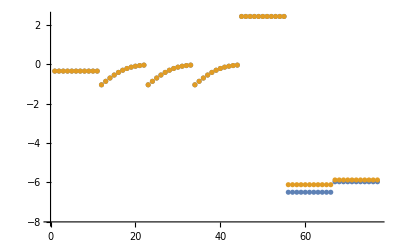

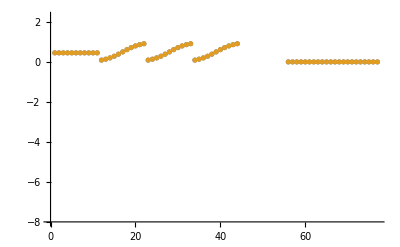

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

-Graphics-

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

-Graphics-

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

-Graphics-

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

-Graphics-

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10